Autor: Antoni Perużyński

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 7

Metoda różnic skończonych

Napisać procedurę realizującą metodę różnic skończonych dla zagadnienia brzegowego liniowego równania różniczkowego zwyczajnego rzędu drugiego. Działanie procedury przetestować na przykładzie podanym na wykładzie.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia brzegowego:

{m y''(x)+ k y'(x) +s y(x)=0,  x∈[0,10],
y(0)=1, y(10)=1,

Obliczenia wykonać dla dwóch zestawów danych:
a) m=1, k=3, s=2;
b) m=5, k=2, s=10.

Za każdym razem obliczenia wykonać dla 500 i 1000 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek oraz zestawić je na wykresie słupkowym, np. postaci:

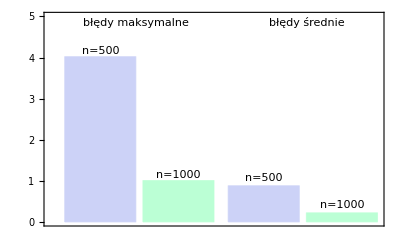

-Graphics-

## Rozwiązanie

```mathematica
Clear[M,K,S,DVec,A,B,Ta,Tb];
RozniceSkonczone[Alpha1_,Alpha2_,Beta1_,Beta2_,M_,K_,S_,DVec_,A_,B_,Ta_,Tb_,number_]:=Module[{alpha1=Alpha1,alpha2=Alpha2,beta1=Beta1,beta2=Beta2,m=M,k=K,s=S,d=DVec,a=A,b=B,ta=Ta,tb=Tb,n=number},
h=(b-a)/(n);
XList=Table[a+i*h,{i,0,n}];
AVector=Table[m[XList[[i]]],{i,1,n}];
BVector=Table[k[XList[[i]]],{i,1,n}];
CVector=Table[s[XList[[i]]],{i,1,n}];
DVector=Table[d[XList[[i]]],{i,1,n}];
(*Define b kreska*)
bResult={2*h*ta};
For[i=2,i≤n,i++,AppendTo[bResult,2*h*h*DVector[[i]]]];
AppendTo[bResult,2*h*tb];
(*Define U*)
U=Table[Table[0,{i,1,n+1}],{j,1,n+1}];
U[[1,1]]=2*h*alpha1-3*alpha2;
U[[1,2]]=4*alpha2;
U[[1,3]]=-alpha2;

For[i=2,i≤n,i++,
U[[i,i-1]]=2*AVector[[i]]-h*BVector[[i]];
U[[i,i]]=2*h*h*CVector[[i]]-4*AVector[[i]];
U[[i,i+1]]=2*AVector[[i]]+h*BVector[[i]];
];

U[[n+1,n-1]]=beta2;
U[[n+1,n]]=-4*beta2;
U[[n+1,n+1]]=2*h*beta1+3*beta2;

result=LinearSolve[U,bResult];
Return[Transpose[{XList,result}]]]
```

### Przykład z wykładu

```mathematica
Alpha1=1;
Alpha2=1;
Beta1=1;
Beta2=1;
M[x_]:=x^2;
K[x_]:=-3*x;
S[x_]:=5;
DVec[x_]:=x^2+5;
A=0;
B=4;
Ta=1;
Tb=25;
number=4;
RozniceSkonczone[Alpha1,Alpha2,Beta1,Beta2,M,K,S,DVec,A,B,Ta,Tb,number]
```

{{0,1},{1,2},{2,5},{3,10},{4,17}}

### Przypadek m=1, k=3, s=2

```mathematica
ClearAll["Global'*"];
Alpha1=1;
Alpha2=0;
Beta1=1;
Beta2=0;
M[x_]:=1;
K[x_]:=3;
S[x_]:=2;
DVec[x_]:=0;
A=0;
B=10;
Ta=1;
Tb=1;
number=500;
```

```mathematica
Clear[y];

accResult=DSolve[{M[x]*y''[x]+K[x]*y'[x]+S[x]*y[x] ==DVec[x], y[0]==1, y[10]==1} , y[x], x];
pacc=Plot[accResult[[1,1,2]],{x,A,B}, PlotStyle->Pink,PlotRange->All];
res500=RozniceSkonczone[Alpha1,Alpha2,Beta1,Beta2,M,K,S,DVec,A,B,Ta,Tb,number];
p500=ListPlot[res500];
res1000=RozniceSkonczone[Alpha1,Alpha2,Beta1,Beta2,M,K,S,DVec,A,B,Ta,Tb,1000];
p1000=ListPlot[res1000];
Show[p500,p1000,pacc]
```

-Graphics-

```mathematica
xw500=Transpose[res500][[1]] ;
yw500=Transpose[res500][[2]] ;
accResultPoints500 = Table[accResult[[1, 1, 2]] /. {x -> xw500[[i]]}, {i, 1,  Length[xw500]}];
bladbezwzgledny500 = Abs[yw500 - accResultPoints500] ;
b500=ListPlot[Transpose[{xw500,bladbezwzgledny500}], PlotStyle->Red, Filling->Axis,PlotRange->Full];
xw1000=Transpose[res1000][[1]] ;
yw1000=Transpose[res1000][[2]] ;
accResultPoints1000 = Table[accResult[[1, 1, 2]] /. {x -> xw1000[[i]]}, {i, 1,  Length[xw1000]}];
bladbezwzgledny1000 = Abs[yw1000 - accResultPoints1000] ;
b1000=ListPlot[Transpose[{xw1000,bladbezwzgledny1000}], PlotStyle->Red, Filling->Axis,PlotRange->Full];
```

-Graphics-

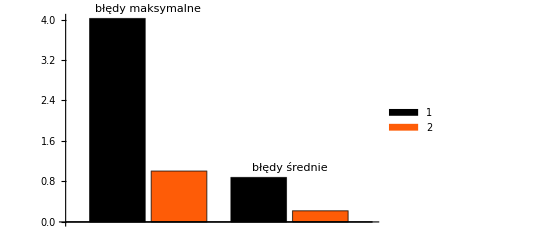

```mathematica
Show[b500,b1000]
BarChart[{{Max[bladbezwzgledny500], Max[bladbezwzgledny1000]}, {Mean[bladbezwzgledny500], Mean[bladbezwzgledny1000]}}, ChartLabels -> {Placed[{"błędy maksymalne", "błędy średnie"},Above],None},ChartStyle-> 3, ChartLegends->{"n=500", "n=1000"}]
```

### Przypadek m=5, k=2, s=10

```mathematica
M[x_]:=5;
K[x_]:=2;
S[x_]:=10;
Clear[y];

accResult=DSolve[{M[x]*y''[x]+K[x]*y'[x]+S[x]*y[x] ==DVec[x], y[0]==1, y[10]==1} , y[x], x];
pacc=Plot[accResult[[1,1,2]],{x,A,B}, PlotStyle->Pink,PlotRange->All];
res500=RozniceSkonczone[Alpha1,Alpha2,Beta1,Beta2,M,K,S,DVec,A,B,Ta,Tb,number];
p500=ListPlot[res500];
res1000=RozniceSkonczone[Alpha1,Alpha2,Beta1,Beta2,M,K,S,DVec,A,B,Ta,Tb,1000];
p1000=ListPlot[res1000];
Show[p500,p1000,pacc]
```

-Graphics-

```mathematica
xw500=Transpose[res500][[1]] ;
yw500=Transpose[res500][[2]] ;
accResultPoints500 = Table[accResult[[1, 1, 2]] /. {x -> xw500[[i]]}, {i, 1,  Length[xw500]}];
bladbezwzgledny500 = Abs[yw500 - accResultPoints500] ;
b500=ListPlot[Transpose[{xw500,bladbezwzgledny500}], PlotStyle->Red, Filling->Axis,PlotRange->Full];
xw1000=Transpose[res1000][[1]] ;
yw1000=Transpose[res1000][[2]] ;
accResultPoints1000 = Table[accResult[[1, 1, 2]] /. {x -> xw1000[[i]]}, {i, 1,  Length[xw1000]}];
bladbezwzgledny1000 = Abs[yw1000 - accResultPoints1000] ;
b1000=ListPlot[Transpose[{xw1000,bladbezwzgledny1000}], PlotStyle->Red, Filling->Axis,PlotRange->Full];
```

-Graphics-

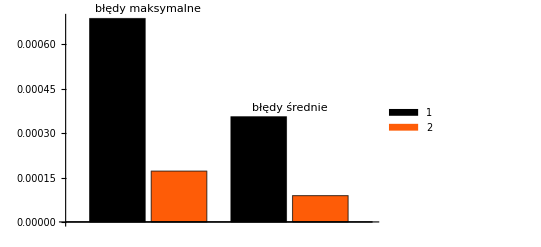

```mathematica
Show[b500,b1000]
BarChart[{{Max[bladbezwzgledny500], Max[bladbezwzgledny1000]}, {Mean[bladbezwzgledny500], Mean[bladbezwzgledny1000]}}, ChartLabels -> {Placed[{"błędy maksymalne", "błędy średnie"},Above],None},ChartStyle-> 3, ChartLegends->{"n=500", "n=1000"}]
```